#### Options

```mathematica
Off[ClebschGordan::tri];
Off[ClebschGordan::phy];
ParallelEvaluate[Off[ClebschGordan::tri]];
ParallelEvaluate[Off[ClebschGordan::phy]];
```

#### Constants

```mathematica
units=Association[cm->Quantity[1,"Centimeters"],um->Quantity[1,"Micrometers"],nm->Quantity[1,"Nanometers"],Hz->Quantity[1,"Hertz"],kHz->Quantity[1,"Kilohertz"],MHz->Quantity[1,"Megahertz"],GHz->Quantity[1,"Gigahertz"],THz->Quantity[1,"Terahertz"],icm->Quantity[1,("Centimeters")^-1],Debye->Quantity[1,"Debyes"],Gauss->Quantity[1,"Gauss"],mV->Quantity[1,"Millivolts"],V->Quantity[1,"Volts"]];
fundamental=Association[ϵ0->Quantity["Permittivity of free space"],ℏ->Quantity["ReducedPlanckConstant"],h->Quantity["PlanckConstant"],μB->Quantity["BohrMagneton"],μN->Quantity["NuclearMagneton"],a0->Quantity[1,"BohrRadius"],c->Quantity["SpeedOfLight"]];
cs=Association[AS12-> h 2.2981579425 GHz,AP12->h 291.9201 MHz,AP32-> h 50.28827 MHz,BP32->-h 0.4934 MHz,CP32-> h 0.560 kHz,ES12-> h 0 MHz,EP12-> h 335.116048807 THz,EP32-> h 351.72571850THz,I1->7/2,S1->1/2,gS->2.0023193043622,gL->0.99999587,gI->-0.00039885395]/.units/.fundamental;
na=Association[AS12-> h 885.81306440 MHz,AP12->h 94.44 MHz,AP32-> h 18.534 MHz,BP32->h 2.724 MHz,CP32-> h 0kHz,ES12-> h 0 MHz,EP12-> h 508.3331958 THz,EP32-> h 508.8487162THz,I1->3/2,S1->1/2,gS->2.0023193043622,gL->0.999976,gI->-0.00080461080]/.units/.fundamental;
experiment=Association[B0->Quantity[0,"Gauss"]];
atom=cs;
constants=Association[{units,fundamental,atom,experiment}];
```

```mathematica
Ahfs=Association[{1/2,1/2,0}->AS12,{1/2,1/2,1}->AP12,{3/2,1/2,1}->AP32];
Bhfs=Association[{3/2,1/2,1}->BP32];
Chfs=Association[{3/2,1/2,1}->CP32];
Efs=Association[{1/2,1/2,0}->ES12,{1/2,1/2,1}->EP12,{3/2,1/2,1}->EP32];
```

```mathematica
Imin=I1/.atom;Imax=I1/.atom;Smin=S1/.atom;Smax=S1/.atom;Lmin=0;Lmax=1;
nℋ=Sum[(2I+1)(2S+1)(2L+1),{I,Imin,Imax},{S,Smin,Smax},{L,Lmin,Lmax}];
ℋ=IdentityMatrix[nℋ];
sℋ=Partition[ℋ,{nℋ,1}][[1]];
bLS={"I","mI","S","mS","L","mL"};
bIJ={"I","mI","J","mJ","S","L"};
bF={"I","F","J","S","L","mF"};
```

```mathematica
lLS=Flatten[Table[bLS/.{"I"->i,"S"->S,"L"->L,"mI"->mI,"mS"->mS,"mL"->mL},{i,Imin,Imax},{S,Smin,Smax},{L,Lmin,Lmax},{mI,-i,i},{mS,-S,S},{mL,-L,L}],5];
lIJ=Flatten[Table[bIJ/.{"I"->i,"S"->S,"L"->L,"J"->J,"mI"->mI,"mJ"->mJ},{i,Imin,Imax},{S,Smin,Smax},{L,Lmin,Lmax},{J,Abs[L-S],L+S},{mI,-i,i},{mJ,-J,J}],5];
lF=Flatten[Table[bF/.{"I"->i,"S"->S,"L"->L,"J"->J,"F"->F,"mF"->mF},{i,Imin,Imax},{S,Smin,Smax},{L,0,Lmax},{J,Abs[L-S],L+S},{F,Abs[i-J],i+J},{mF,-F,F}],5];
b2l=AssociationThread[{bLS,bIJ,bF}->{lLS,lIJ,lF}];
```

```mathematica
b2b[bTo_,bFrom_,qTo_,qFrom_]:=With[{lTo=b2l[bTo],lFrom=b2l[bFrom],pFrom=Position[bFrom,#][[1,1]]&/@qFrom,pTo=Position[bTo,#][[1,1]]&/@qTo,pnTo=Position[bTo,#][[1,1]]&/@Intersection[bTo,bFrom],
pnFrom=Position[bFrom,#][[1,1]]&/@Intersection[bTo,bFrom]},Table[With[{to=lTo[[r]],from=lFrom[[c]]},If[to[[pnTo]]!=from[[pnFrom]],0,ClebschGordan[to[[pTo[[1;;2]]]],to[[pTo[[3;;4]]]],from[[pFrom]]]]],{r,Length[lTo]},{c,Length[lFrom]}]];
```

```mathematica
IJ2LS=b2b[bLS,bIJ,{"S","mS","L","mL"},{"J","mJ"}];
F2IJ=b2b[bIJ,bF,{"J","mJ","I","mI"},{"F","mF"}];
F2LS=IJ2LS.F2IJ;
LS2IJ=IJ2LS†;
IJ2F=F2IJ†;
LS2F=F2LS†;
```

```mathematica
UnitaryMatrixQ/@{IJ2LS,F2IJ,F2LS,LS2IJ,IJ2F,LS2F}
```

{True,True,True,True,True,True}

H_hfs=A_hfs I·J+B_hfs(3(I·J)^2+3/2(I·J)-I(I+1)J(J+1))/(2I(2I-1)J(2J-1))+C_hfs(10(I·J)^3+20(I·J)^2+2(I·J)[I(I+1)+J(J+1)+3-3I(I+1)J(J+1)]-5I(I+1)J(J+1))/(I(I-1)(2I-1)J(J-1)(2J-1))
H_B=μ_B/ℏ(g_s S+g_L L+g_I I)·B

```mathematica
J1dotJ2[J_,J1_,J2_]:=1/2(J(J+1)-J1(J1+1)-J2(J2+1))
```

```mathematica
HhfFC=With[{p=Position[bF,#][[1,1]]&/@{"F","I","J","S","L"}},DiagonalMatrix[Table[With[{F=lF[[n,p[[1]]]],I=lF[[n,p[[2]]]],J=lF[[n,p[[3]]]],JSL=lF[[n,p[[3;;5]]]]},
Ahfs[JSL]J1dotJ2[F,I,J]+If[J==1/2,0,Bhfs[JSL](3 J1dotJ2[F,I,J]^2+3/2 J1dotJ2[F,I,J]-I(I+1)J(J+1))/(2I(2I-1)J(2J-1))+Chfs[JSL]((10 J1dotJ2[F,I,J]^3+20 J1dotJ2[F,I,J]^2+2J1dotJ2[F,I,J](I(I+1)+J(J+1)+3-3I(I+1)J(J+1))-5I(I+1)J(J+1))/(I(I-1)(2I-1)J(J-1)(2J-1)))]]
,{n,1,nℋ}]]];
HfIJ=With[{p=Position[bIJ,#][[1,1]]&/@{"J","S","L"}},DiagonalMatrix[Table[With[{JSL=lIJ[[n,p]]},Efs[JSL]],{n,1,nℋ}]]];
```

```mathematica
HZLS=With[{p=Position[bLS,#][[1,1]]&/@{"mS","mL","mI"}},DiagonalMatrix[Table[With[{mS=lLS[[n,p[[1]]]],mL=lLS[[n,p[[2]]]],mI=lLS[[n,p[[3]]]]},μB B0(gS mS+gL mL+gI mI)],{n,1,nℋ}]]];
HIJ=(LS2IJ.HZLS.IJ2LS)+HfIJ+F2IJ.HhfFC.IJ2F;
HF=(LS2F.HZLS.F2LS)+IJ2F.HfIJ.F2IJ+HhfFC;
```

```mathematica
findBasisState[qn_,basis_]:=With[{labels=qn[[All,1]],numbers=qn[[All,2]]},Flatten[Position[b2l[basis][[All,Flatten[labels/.PositionIndex[basis]]]],numbers]]]
findEigenState[qn_,eigs_,basis_]:=Module[{pos,e2b,foundEigs},pos=findBasisState[qn,basis];foundEigs=OrderingBy[eigs[[2,All,pos]],Total[Abs[#]^2]&][[-Length[pos];;-1]];foundEigs[[Ordering@eigs[[1,foundEigs]]]]]
findSystem[rep_,qn_,HBasis_,basis_]:=Module[{H0,e0,states},H0=QuantityMagnitude[UnitConvert[HBasis/h/.rep//.constants]];e0=Sort[Eigensystem[H0]ᵀ]ᵀ]
findStates[rep_,qn_,HBasis_,basis_]:=Module[{H0,e0,states},H0=QuantityMagnitude[UnitConvert[HBasis/h/.rep//.constants]];e0=Sort[Eigensystem[H0]ᵀ]ᵀ;
states=findEigenState[qn,e0,basis];
e0[[1,states]]]
findEnergy[eBasis_,bBasis_,lTarget_,bTarget_]:=Module[{evecsL,lClosest,lError,eClosest},
evecsL=((eBasis[[2]]^2).b2l[bBasis])[[All,Flatten[PositionIndex[bBasis]/@bTarget]]];
lClosest=Nearest[evecsL,lTarget][[1]];
lError=lTarget-lClosest;
eClosest=eBasis[[1]][[Position[evecsL,lClosest][[1,1]]]];
{eClosest,lError}
]
```

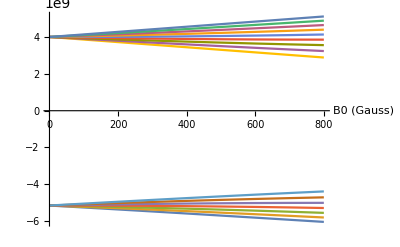

```mathematica
scanParameter=B0;
scanUnit=Gauss;
scan=Range[0,860,100];

tab=ParallelTable[findStates[{scanParameter->x scanUnit},{"L"->0,"J"->1/2},HIJ,bIJ],{x,scan}]ᵀ;
tab=(Transpose@{scan,#}&/@tabᵀ)ᵀ;
ListPlot[tab,Joined->True,AxesLabel->{StringForm["`` (``)",scanParameter,scanUnit]}]
```

```mathematica
rep0={B0->800Gauss};
eIJ=Eigensystem[HIJ/h/.rep0/.constants//UnitConvert//QuantityMagnitude];
eF=Eigensystem[HF/h/.rep0/.constants//UnitConvert//QuantityMagnitude];
eIJ=Sort[eIJᵀ]ᵀ;
eF=Sort[eFᵀ]ᵀ;
```

```mathematica
b800=With[{nf=4,ni=3},Table[If[Abs[mf-mi]<=1,(findEnergy[eF,bF,{0,nf,mf}, {"L","F","mF"}]-findEnergy[eF,bF,{0,ni,mi}, {"L","F","mF"}])[[1]],0],{mf,-nf,nf},{mi,-ni,ni}]]ᵀ
```

{{7.30347×10^9,7.65585×10^9,7.97836×10^9,0,0,0,0,0,0},{0,7.97925×10^9,8.30175×10^9,8.60088×10^9,0,0,0,0,0},{0,0,8.60177×10^9,8.9009×10^9,9.1811×10^9,0,0,0,0},{0,0,0,9.18199×10^9,9.46219×10^9,9.72665×10^9,0,0,0},{0,0,0,0,9.72754×10^9,9.992×10^9,1.02431×10^10,0,0},{0,0,0,0,0,1.0244×10^10,1.04951×10^10,1.07347×10^10,0},{0,0,0,0,0,0,1.07356×10^10,1.09752×10^10,1.12047×10^10}}

```mathematica
b801-b800//MatrixForm
```

(-2.25244×10^6 | -1.70293×10^6 | -1.2492×10^6 | 0 | 0 | 0 | 0 | 0 | 0
0 | -1.24808×10^6 | -794341. | -406281. | 0 | 0 | 0 | 0 | 0
0 | 0 | -405164. | -17104.4 | 323233. | 0 | 0 | 0 | 0
0 | 0 | 0 | 324350. | 664687. | 968828. | 0 | 0 | 0
0 | 0 | 0 | 0 | 969945. | 1.27409×10^6 | 1.54985×10^6 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1.55096×10^6 | 1.82673×10^6 | 2.07964×10^6 | 0
0 | 0 | 0 | 0 | 0 | 0 | 2.08076×10^6 | 2.33368×10^6 | 2.56781×10^6)